```mathematica
Imp=Import["/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/schrodinger_999.dat"]
```

{{-99.8,9.17634×10^-14,3.26574×10^-7,0.000130989,-0.000303592},{-99.6,1.83482×10^-13,6.53291×10^-7,0.000261979,-0.000607173},{-99.4,2.7511×10^-13,9.80295×10^-7,0.000392972,-0.00091073},994,{99.6,1.7471×10^-13,-6.53255×10^-7,0.00026198,0.000607173},{99.8,8.73762×10^-14,-3.26556×10^-7,0.000130989,0.000303592}}
 |  |  |  |

```mathematica
mat=Table[Imp]
```

{{-99.8,9.17634×10^-14,3.26574×10^-7,0.000130989,-0.000303592},{-99.6,1.83482×10^-13,6.53291×10^-7,0.000261979,-0.000607173},{-99.4,2.7511×10^-13,9.80295×10^-7,0.000392972,-0.00091073},994,{99.6,1.7471×10^-13,-6.53255×10^-7,0.00026198,0.000607173},{99.8,8.73762×10^-14,-3.26556×10^-7,0.000130989,0.000303592}}
 |  |  |  |

```mathematica
plot1=mat[[All, {1,2}]];
```

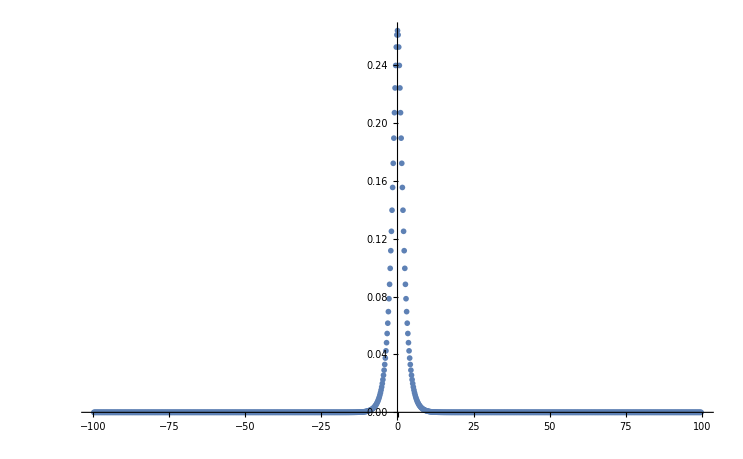

```mathematica
fig1=ListPlot[plot1, PlotRange->All]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/vetor1.pdf", fig1 , "PDF"]
```

/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/vetor1.pdf

```mathematica
plot2=mat[[All, {1,3}]];
```

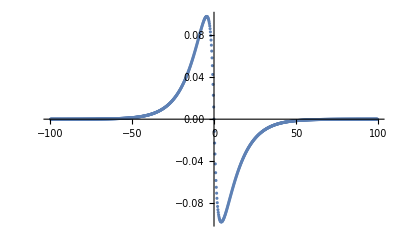

```mathematica
fig2=ListPlot[plot2, PlotRange->All]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/vetor2.pdf", fig2 , "PDF"]
```

/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/vetor2.pdf

```mathematica
plot3=mat[[All, {1,4}]];
```

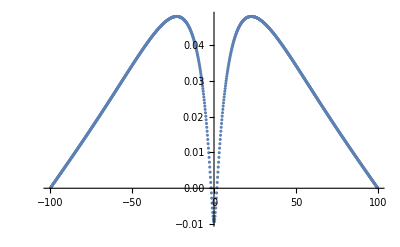

```mathematica
fig3=ListPlot[plot3, PlotRange->All]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/vetor3.pdf", fig3 , "PDF"]
```

/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/vetor3.pdf

```mathematica
plot4=mat[[All, {1,5}]];
```

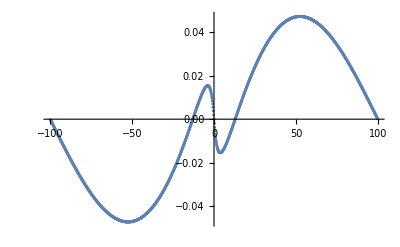

```mathematica
fig4=ListPlot[plot4, PlotRange->All]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/vetor4.pdf", fig4 , "PDF"]
```

/home/mariana/Documentos/Ano_2/FComputacional/Lab/Git_Projetos/P4/vetor4.pdf